```mathematica
riemannPrimeCount[n_]:=Sum[k^-1 PrimePi[n^(1/k)],{k, 1,Log[2,n]}]
Table[{n,riemannPrimeCount[n]},{n,1,100}]//TableForm
```

1 | 0
2 | 1
3 | 2
4 | 5/2
5 | 7/2
6 | 7/2
7 | 9/2
8 | 29/6
9 | 16/3
10 | 16/3
11 | 19/3
12 | 19/3
13 | 22/3
14 | 22/3
15 | 22/3
16 | 91/12
17 | 103/12
18 | 103/12
19 | 115/12
20 | 115/12
21 | 115/12
22 | 115/12
23 | 127/12
24 | 127/12
25 | 133/12
26 | 133/12
27 | 137/12
28 | 137/12
29 | 149/12
30 | 149/12
31 | 161/12
32 | 817/60
33 | 817/60
34 | 817/60
35 | 817/60
36 | 817/60
37 | 877/60
38 | 877/60
39 | 877/60
40 | 877/60
41 | 937/60
42 | 937/60
43 | 997/60
44 | 997/60
45 | 997/60
46 | 997/60
47 | 1057/60
48 | 1057/60
49 | 1087/60
50 | 1087/60
51 | 1087/60
52 | 1087/60
53 | 1147/60
54 | 1147/60
55 | 1147/60
56 | 1147/60
57 | 1147/60
58 | 1147/60
59 | 1207/60
60 | 1207/60
61 | 1267/60
62 | 1267/60
63 | 1267/60
64 | 1277/60
65 | 1277/60
66 | 1277/60
67 | 1337/60
68 | 1337/60
69 | 1337/60
70 | 1337/60
71 | 1397/60
72 | 1397/60
73 | 1457/60
74 | 1457/60
75 | 1457/60
76 | 1457/60
77 | 1457/60
78 | 1457/60
79 | 1517/60
80 | 1517/60
81 | 383/15
82 | 383/15
83 | 398/15
84 | 398/15
85 | 398/15
86 | 398/15
87 | 398/15
88 | 398/15
89 | 413/15
90 | 413/15
91 | 413/15
92 | 413/15
93 | 413/15
94 | 413/15
95 | 413/15
96 | 413/15
97 | 428/15
98 | 428/15
99 | 428/15
100 | 428/15

```mathematica
Zk[n_,k_,s_]:=Sum[j^-s Zk[n/j,k-1,s],{j,1,n}];Zk[n_,0,s_]:=UnitStep[n-1]
Table[Zk[n,k,0],{n,1,50},{k,1,7}]//TableForm
```

1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 3 | 4 | 5 | 6 | 7 | 8
3 | 5 | 7 | 9 | 11 | 13 | 15
4 | 8 | 13 | 19 | 26 | 34 | 43
5 | 10 | 16 | 23 | 31 | 40 | 50
6 | 14 | 25 | 39 | 56 | 76 | 99
7 | 16 | 28 | 43 | 61 | 82 | 106
8 | 20 | 38 | 63 | 96 | 138 | 190
9 | 23 | 44 | 73 | 111 | 159 | 218
10 | 27 | 53 | 89 | 136 | 195 | 267
11 | 29 | 56 | 93 | 141 | 201 | 274
12 | 35 | 74 | 133 | 216 | 327 | 470
13 | 37 | 77 | 137 | 221 | 333 | 477
14 | 41 | 86 | 153 | 246 | 369 | 526
15 | 45 | 95 | 169 | 271 | 405 | 575
16 | 50 | 110 | 204 | 341 | 531 | 785
17 | 52 | 113 | 208 | 346 | 537 | 792
18 | 58 | 131 | 248 | 421 | 663 | 988
19 | 60 | 134 | 252 | 426 | 669 | 995
20 | 66 | 152 | 292 | 501 | 795 | 1191
21 | 70 | 161 | 308 | 526 | 831 | 1240
22 | 74 | 170 | 324 | 551 | 867 | 1289
23 | 76 | 173 | 328 | 556 | 873 | 1296
24 | 84 | 203 | 408 | 731 | 1209 | 1884
25 | 87 | 209 | 418 | 746 | 1230 | 1912
26 | 91 | 218 | 434 | 771 | 1266 | 1961
27 | 95 | 228 | 454 | 806 | 1322 | 2045
28 | 101 | 246 | 494 | 881 | 1448 | 2241
29 | 103 | 249 | 498 | 886 | 1454 | 2248
30 | 111 | 276 | 562 | 1011 | 1670 | 2591
31 | 113 | 279 | 566 | 1016 | 1676 | 2598
32 | 119 | 300 | 622 | 1142 | 1928 | 3060
33 | 123 | 309 | 638 | 1167 | 1964 | 3109
34 | 127 | 318 | 654 | 1192 | 2000 | 3158
35 | 131 | 327 | 670 | 1217 | 2036 | 3207
36 | 140 | 363 | 770 | 1442 | 2477 | 3991
37 | 142 | 366 | 774 | 1447 | 2483 | 3998
38 | 146 | 375 | 790 | 1472 | 2519 | 4047
39 | 150 | 384 | 806 | 1497 | 2555 | 4096
40 | 158 | 414 | 886 | 1672 | 2891 | 4684
41 | 160 | 417 | 890 | 1677 | 2897 | 4691
42 | 168 | 444 | 954 | 1802 | 3113 | 5034
43 | 170 | 447 | 958 | 1807 | 3119 | 5041
44 | 176 | 465 | 998 | 1882 | 3245 | 5237
45 | 182 | 483 | 1038 | 1957 | 3371 | 5433
46 | 186 | 492 | 1054 | 1982 | 3407 | 5482
47 | 188 | 495 | 1058 | 1987 | 3413 | 5489
48 | 198 | 540 | 1198 | 2337 | 4169 | 6959
49 | 201 | 546 | 1208 | 2352 | 4190 | 6987
50 | 207 | 564 | 1248 | 2427 | 4316 | 7183

```mathematica
Zk1[n_,s_]:=Sum[j^-s,{j,1,n}]
Zk2[n_,s_]:=Sum[j^-s k^-s,{j,1,n},{k,1,n/j}]
Zk3[n_,s_]:=Sum[j^-s k^-s m^-s,{j,1,n},{k,1,n/j},{m,1,n/(j k)}]
Zk[n_,k_,s_]:=Sum[j^-s Zk[n/j,k-1,s],{j,1,n}];Zk[n_,0,s_]:=UnitStep[n-1]
FullSimplify[Table[{Zk1[n,s]-Zk[n,1,s],Zk2[n,s]-Zk[n,2,s],Zk3[n,s]-Zk[n,3,s]},{n,1,50}]//TableForm]
```

0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
ds[n_,k_,s_] := ds[n,k,s]=Sum[ j^-s ds[Floor[n/j],k-1,s],{j,2,n}]; ds[n_,0,s_]:=UnitStep[n-1]
dz[n_, z_, s_] := Expand[Sum[ bin[z,k] ds[n,k,s],{k,0,Log[2,n]}]]
zeros[n_,s_]:=List@@Roots[dz[n,z,s]==0,z][[All,2]]
```

```mathematica
FullSimplify[dz[100,z,-1/5]]
```

$Aborted

```mathematica
((1/(Zeta[s])-1)-FullSimplify[Sum[ (-1)^k (Zeta[s]-1)^k,{k,1,Infinity}]])
```

0

```mathematica
1/(Zeta[s])-1
```

-1+1/Zeta[s]

```mathematica
Sum[ (-1)^j (Zeta[s]-1)^(j+k),{j,0,Infinity}]
```

(-1+Zeta[s])^k/Zeta[s]

```mathematica
FullSimplify[-(Zeta[s]^-1 - 1 )( (Zeta[s]-1)^k + (Zeta[s]-1)^(k-1) )]
```

(-1+Zeta[s])^k

```mathematica
Sum[ (-1)^(k+1)/k (Zeta[s]-1)^(k+a),{k,1,Infinity}]
```

Log[Zeta[s]] (-1+Zeta[s])^a

```mathematica
(Zeta[s]-1)^a (Zeta[s]-1)^k
```

(-1+Zeta[s])^(a+k)

```mathematica
FullSimplify[(Zeta[s]-1)( -(Zeta[s]^-1-1)^(k-1)-(Zeta[s]^-1-1)^k)]
```

(-1+1/Zeta[s])^k

```mathematica
FullSimplify[Sum[ (-1)^(k+j) Binomial[ k+j-1, k-1] (Zeta[s]-1)^(k+j),{j,0, Infinity}]]
```

(-1)^k (1-1/Zeta[s])^k

```mathematica
FullSimplify[Sum[(-1)^(k)/k (Zeta[s]^-1-1)^(k),{k,1,Infinity}]]
```

-Log[1/Zeta[s]]

```mathematica
Sum[ (-1)^a Binomial[a,b] (Zeta[s]^-1 -1)^a (Zeta[s]-1)^(k-b),{b,0,a}]
```

(-1+Zeta[s])^k

```mathematica
Sum[ (-1)^(k+1)/k (Zeta[s]-1)^k Log[ Zeta[s]]^(a-1),{k,1,Infinity}]
```

Log[Zeta[s]]^a

```mathematica
N[Log[Zeta[3]]^4]
```

0.00114708

```mathematica
Sum[ Log[ Zeta[s]]^{a+k},{k,1,Infinity}]
```

{-Log[Zeta[s]]^(1+a)/(-1+Log[Zeta[s]])}

```mathematica
(Zeta[s]-1) (Log[Zeta[s]])^a
```

Log[Zeta[s]]^a (-1+Zeta[s])

```mathematica
Series[(1/(Log[x+1]+1)-1)^2,{x,0,10}]
```

x^2-3 x^3+(83 x^4)/12-(43 x^5)/3+(2521 x^6)/90-(791 x^7)/15+(81251 x^8)/840-(187979 x^9)/1080+(61723 x^10)/200+O[x]^11

```mathematica
Series[(1/(Log[x+1]+1))^2,{x,0,10}]
```

1-2 x+4 x^2-(23 x^3)/3+(57 x^4)/4-(259 x^5)/10+(2777 x^6)/60-(1714 x^7)/21+(19937 x^8)/140-(372413 x^9)/1512+(7992833 x^10)/18900+O[x]^11

```mathematica
FullSimplify[((Log[x+1]+1)^-1-1)]
```

-1+1/(1+Log[1+x])

```mathematica
Series[(1/(x+1)-1)^1,{x,0,10}]
```

-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10+O[x]^11

```mathematica
Series[(1/(Log[x+1]+1)-1),{x,0,10}]
```

-x+(3 x^2)/2-(7 x^3)/3+(11 x^4)/3-(347 x^5)/60+(3289 x^6)/360-(1011 x^7)/70+(38371 x^8)/1680-(136553 x^9)/3780+(4320019 x^10)/75600+O[x]^11

```mathematica
Series[((Log[x+1]+1)^-1),{x,0,10}]
```

1-x+(3 x^2)/2-(7 x^3)/3+(11 x^4)/3-(347 x^5)/60+(3289 x^6)/360-(1011 x^7)/70+(38371 x^8)/1680-(136553 x^9)/3780+(4320019 x^10)/75600+O[x]^11

```mathematica
(((Log[x+1]+1)^-1))(Log[x+1]+1)
```

1

```mathematica
K[n_]:=FullSimplify[MangoldtLambda[n]/Log[n]]
logD[n_,k_]:=logD[n,k]=Sum[K[j] logD[Floor[n/j],k-1],{j,2,n}];logD[n_,0]:=UnitStep[n-1]
logDz[n_, z_] := Sum[ bin[z,k] logD[n,k],{k,0,Log[2n]}]
```

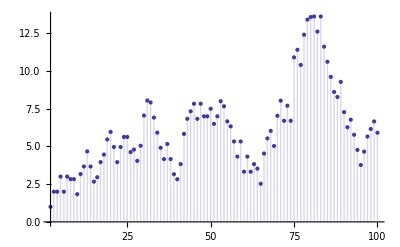

```mathematica
DiscretePlot[D[Expand[logDz[n,z]],{z,1}]/.z->0,{n,2,100}]
```

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
K[n_]:=FullSimplify[MangoldtLambda[n]/Log[n]]
logD[n_,k_,s_]:=logD[n,k,s]=Sum[If[ K[j] == 0, 0, (-1)^(j+1)j^-s K[j] logD[Floor[n/j],k-1,s]],{j,2,n}];logD[n_,0,s_]:=UnitStep[n-1]
logDz[n_, z_,s_] := Sum[ bin[z,k] logD[n,k,s],{k,0,Log[2n]}]
Dz[n_, z_,s_] := Sum[ z^k/k! logD[n,k,s],{k,0,Log[2n]}]
zeros[n_,s_]:=List@@NRoots[Dz[n,z,s]==0,z][[All,2]]
```

```mathematica
Dz[100,1,-1]
```

45442/9

```mathematica
Table[ {N[logD[100,k,2]],N[Log[Zeta[2]]^k]},{k,0,14}]
```

{{1.,1.},{0.495776,0.4977},{0.240154,0.247706},{0.105174,0.123283},{0.0369013,0.0613581},{0.00755238,0.0305379},{0.000895182,0.0151987},{0.,0.00756441},{0.,0.00376481},{0.,0.00187375},{0.,0.000932565},{0.,0.000464138},{0.,0.000231002},{0.,0.00011497},{0.,0.0000572204}}

```mathematica
zeros[ 100, ZetaZero[1]]
```

{-2.62683-0.291815 ⅈ,0.982159+4.91784 ⅈ,1.12502-0.282495 ⅈ,1.6139-2.81973 ⅈ,1.86201+0.66778 ⅈ}

```mathematica
Log[2,10000.]
```

13.2877

```mathematica
Product[ 1-(1/j),{j,zeros[ 10000,2]}]
```

0.92525+1.38778×10^-17 ⅈ

```mathematica
N[ Dz[10000,1,ZetaZero[1]]]
```

$Aborted

```mathematica
N[Pi^2/6]
```

1.64493

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
filt[ n_, m_] := Sum[ If[ Log[j,n] == Floor[Log[j,n]],1,0],{j,2,m}]
Ka[n_,m_]:=If[ filt[n,m]>0,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
logDa[n_,k_,s_,m_]:=logDa[n,k,s]=Sum[If[ Ka[j,m] == 0, 0, j^-s Ka[j,m] logDa[Floor[n/j],k-1,s,m]],{j,2,n}];logDa[n_,0,s_,m_]:=UnitStep[n-1]
logDaz[n_, z_,s_,m_] := Sum[ bin[z,k] logDa[n,k,s,m],{k,0,Log[2n]}]
Daz[n_, z_,s_,m_] := Sum[ z^k/k! logDa[n,k,s,m],{k,0,Log[2n]}]
zerosa[n_,s_,m_]:=List@@NRoots[Daz[n,z,s,m]==0,z][[All,2]]
```

```mathematica
logDa[100,1,0]+HarmonicNumber[ Floor[Log[2,100]]]+HarmonicNumber[ Floor[Log[3,100]]]+HarmonicNumber[ Floor[Log[5,100]]]
```

181/30+logDa[100,1,0]

```mathematica
HarmonicNumber[ Floor[Log[2,100]]]
```

49/20

```mathematica
zerosa[ 1000,0,1]
```

{-4.8878,-4.13806-5.52305 ⅈ,-4.13806+5.52305 ⅈ,-2.05117-1.10317 ⅈ,-2.05117+1.10317 ⅈ,-0.961669,-0.00572997}

```mathematica
zerosa[ 1000,0,2]
```

{-265.031,-10.7617-2.65172 ⅈ,-10.7617+2.65172 ⅈ,-3.27504,-1.16496,-0.0057963}

```mathematica
zerosa[ 1000,0,3]
```

{-69.8934,-8.28722,-1.41355,-0.00586255}

```mathematica
zerosa[ 1000,0,5]
```

{-32.9481,-1.92101,-0.00592479}

```mathematica
zerosa[ 1000,0,7]
```

{-2.80914,-0.00598286}

```mathematica
zerosa[ 1000,0,11]
```

{-4.14397,-0.00603287}

```mathematica
zerosa[ 1000,0,13]
```

{-6.7082,-0.00608454}

```mathematica
zerosa[ 1000,0,17]
```

{-10.8605,-0.00613844}

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Dz[n_,z_,k_,s_]:=Dz[n,z,k,s]=1+((z+1)/k-1)Sum[(-1)^(j+1)j^-s Dz[n/j,z,k+1,s],{j,2,n}]
zeros[n_,s_]:=List@@NRoots[Dz[n,z,1,s]==0,z][[All,2]]
```

```mathematica
Expand[Dz[100,z,1,N[ZetaZero[1]]]]
```

1-(0.764664-0.423453 ⅈ) z-(0.694574+0.47739 ⅈ) z^2+(0.612768+0.0349837 ⅈ) z^3-(0.129055-0.0723845 ⅈ) z^4+(0.0100174-0.0179348 ⅈ) z^5-(0.000011119-0.000708482 ⅈ) z^6

```mathematica
zeros[5000,N[ZetaZero[1]]]
```

{-0.122278-0.302615 ⅈ,0.988031+0.000854469 ⅈ,1.66008-3.88178 ⅈ,1.97964-0.321138 ⅈ,1.9824+0.266293 ⅈ,2.05348+4.00239 ⅈ,3.50892+13.7615 ⅈ,6.35835-1.05213 ⅈ,9.92667-1.40671 ⅈ,31.9434+42.1149 ⅈ,43.9777-15.061 ⅈ,111.277-542.104 ⅈ}

```mathematica
zeros[1000,.1 + N[ZetaZero[1]]]
```

{-2.58444+1.07135 ⅈ,0.744939-0.749314 ⅈ,0.844225+0.853938 ⅈ,2.04714-0.675841 ⅈ,2.16373+0.8309 ⅈ,4.88379-0.62227 ⅈ,11.5722-1.88375 ⅈ,17.1958+15.5409 ⅈ,89.5536-52.2708 ⅈ}

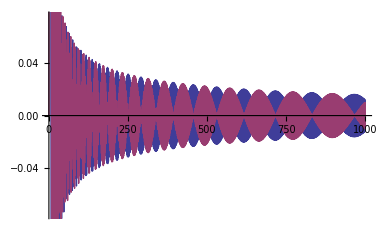

```mathematica
DiscretePlot[{Re[Dz[n,1,1,N[ZetaZero[2]]]],Im[Dz[n,1,1,N[ZetaZero[2]]]]},{n,1,1000}]
```

```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FI[n]=FactorInteger[n];FI[1]:={}
Dz1[n_, z_, s_] := Dz1[n,z,s]=Sum[FullSimplify[ j^-s  dz[j,z]],{j,1,n}]
DxDAlt[n_,z_,x_,s_]:=Sum[(-1)^j bin[z,j] x^(j(1-s)) Dz1[n/x^j,z,s],{j,0,Log[x,n]}]
zeros2[n_,s_]:=List@@NRoots[DxDAlt[n,z,2,s]==0,z][[All,2]]
zeros3[n_,s_]:=List@@Roots[DxDAlt[n,z,2,s]==0,z][[All,2]]
```

```mathematica
Expand[Dz1[100000,z,0]]
```

1+(991892879 z)/102960+(16611877533197 z^2)/605404800+(27613425421567 z^3)/864864000+(8883298064606291 z^4)/435891456000+(82938597121 z^5)/10264320+(12123475378339 z^6)/5748019200+(987114594581 z^7)/2612736000+(6832898553167 z^8)/146313216000+(53237749 z^9)/13063680+(1772592397 z^10)/7315660800+(20466961 z^11)/2052864000+(30323737 z^12)/114960384000+(841 z^13)/186810624+(9773 z^14)/209227898880+(71 z^15)/373621248000+(17 z^16)/20922789888000

```mathematica
DxDAlt[ 1231, 1.5,2,-1]
```

-1796.7

```mathematica
Dz[1231,1.5,1,-1]
```

-1796.7

```mathematica
Expand[DxDAlt[100000,z,2,0]]
```

1+(63100897 z)/80080-(180348209849 z^2)/55036800+(97254541679083 z^3)/18162144000-(397875843476297 z^4)/87178291200+(819629656441 z^5)/359251200-(90242719681 z^6)/127733760+(359231217229 z^7)/2612736000-(162434105119 z^8)/9754214400+(71104889 z^9)/57153600-(15739609 z^10)/270950400+(23627123 z^11)/14370048000-(487 z^12)/15482880+(1063 z^13)/1334361600-(6373 z^14)/348713164800+(433 z^15)/2615348736000-z^16/1394852659200

```mathematica
zeros2[100000,N[ZetaZero[1]]]
```

{-1.5782+2.56046 ⅈ,0.099237-0.00129244 ⅈ,1.00102+0.000529329 ⅈ,1.51313-8.06227 ⅈ,1.97177-0.010541 ⅈ,2.9512+1.09857 ⅈ,3.05508-1.61428 ⅈ,3.39272+0.0222148 ⅈ,5.55241-0.00674025 ⅈ,10.2484+11.7983 ⅈ,13.0121+44.0801 ⅈ,16.1591+2.96883 ⅈ,17.1949-9.11333 ⅈ,43.7242-21.1622 ⅈ,120.418-118.71 ⅈ,121.553+200.507 ⅈ}

```mathematica
zeros2[100000,.1+N[ZetaZero[1]]]
```

{-1.58961+2.61753 ⅈ,0.433581-0.213656 ⅈ,0.5472+0.271463 ⅈ,1.47342-7.99666 ⅈ,2.08921-0.0510959 ⅈ,2.94335+1.09229 ⅈ,3.05787-1.61562 ⅈ,3.38832+0.0294925 ⅈ,5.55214-0.00687741 ⅈ,10.2124+11.7658 ⅈ,13.1309+44.1903 ⅈ,16.1775+3.07072 ⅈ,17.0161-9.05257 ⅈ,43.7773-20.9222 ⅈ,120.592-118.335 ⅈ,122.483+202.34 ⅈ}

```mathematica
zeros2[100000,.1I+N[ZetaZero[1]]]
```

{-1.64513+2.54763 ⅈ,0.0321829+0.0859746 ⅈ,1.11228-0.0735677 ⅈ,1.44684-8.10087 ⅈ,1.91921-0.0420792 ⅈ,2.96582+1.09079 ⅈ,3.04473-1.60261 ⅈ,3.38918+0.0248579 ⅈ,5.55256-0.00702265 ⅈ,10.2845+11.7613 ⅈ,12.9031+44.1993 ⅈ,16.058+2.98967 ⅈ,17.1283-9.28908 ⅈ,43.4956-21.1092 ⅈ,119.73+201.411 ⅈ,120.056-118.551 ⅈ}

```mathematica
zeros2[100000,N[ZetaZero[2]]]
```

{-11.5782+180.192 ⅈ,-5.18725-11.1497 ⅈ,0.0992719+0.0123424 ⅈ,0.997808-0.000207433 ⅈ,1.93441+0.181163 ⅈ,1.94229-0.220858 ⅈ,2.34694+47.1573 ⅈ,2.80181-2.37204 ⅈ,2.99031+2.103 ⅈ,3.44301-0.0212634 ⅈ,5.5488-0.0375321 ⅈ,9.0019+16.1821 ⅈ,11.0893+2.21452 ⅈ,11.28-14.7059 ⅈ,39.5162-32.7796 ⅈ,106.874-160.032 ⅈ}

```mathematica
FullSimplify[DxDAlt[100000,z,2,0]]
```

-1/20922789888000(-1+z) (20922789888000+z (16507521312307200+z (-52053654143888640+z (59983577870414976+z (-35506624563896304+z (12228606627227536+z (-2553150856520264+z (323572731049568+z (-24848424430687+z (1181653334433+z (-33759272547+z (641818541+z (-16288909+z (378931+z (-3449+15 z)))))))))))))))

```mathematica
FullSimplify[DxDAlt[100,z,2,ZetaZero[1]]]
```

$Aborted

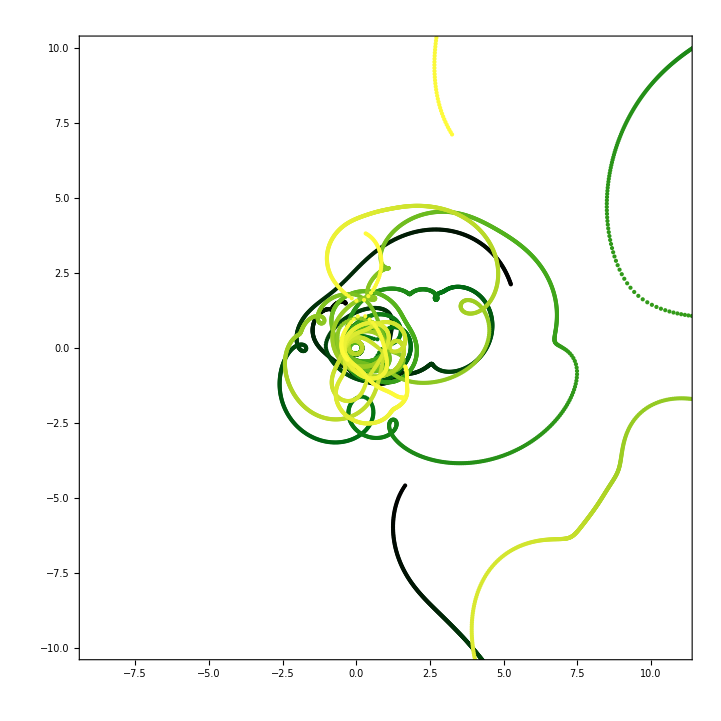

```mathematica
colfunc=ColorData["AvocadoColors"]; aa = 0;bb = 1600;
pts1=Table[{colfunc[(n-aa)/bb],Point[{Re[#],Im[#]}]}&/@zeros2[100, n*.02I+N[ZetaZero[12]]],{n,aa,aa+bb}];
Graphics[pts1,Frame->True,PlotRange->{{-10+1,10+1},{-10,10}}]
```

```mathematica
N[ZetaZero[45]]
```

0.5+133.498 ⅈ

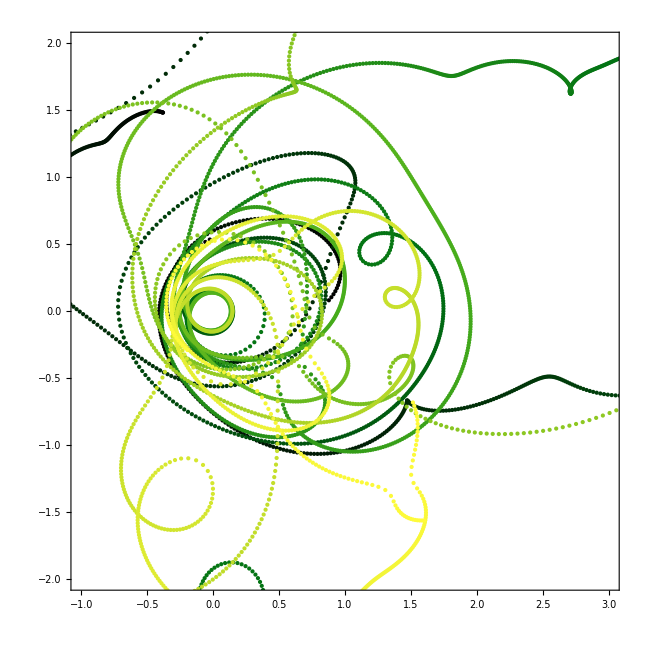

```mathematica
colfunc=ColorData["AvocadoColors"]; aa = 0;bb = 1600;
pts1=Table[{colfunc[(n-aa)/bb],Point[{Re[#],Im[#]}]}&/@zeros2[100, -.1+n*.02I+N[ZetaZero[12]]],{n,aa,aa+bb}];
Graphics[pts1,Frame->True,PlotRange->{{-2+1,2+1},{-2,2}}]
```

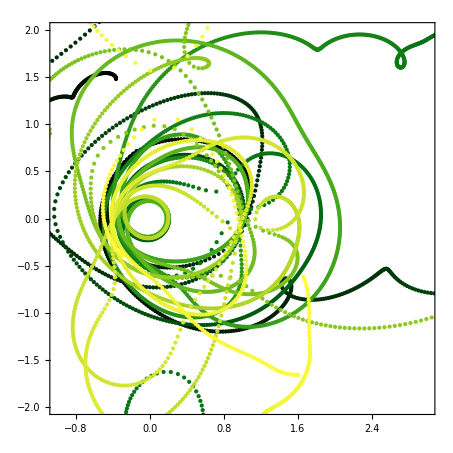

```mathematica
colfunc=ColorData["AvocadoColors"]; aa = 0;bb = 1600;
pts1=Table[{colfunc[(n-aa)/bb],Point[{Re[#],Im[#]}]}&/@zeros2[100, n*.02I+N[ZetaZero[12]]],{n,aa,aa+bb}];
Graphics[pts1,Frame->True,PlotRange->{{-2+1,2+1},{-2,2}}]
```

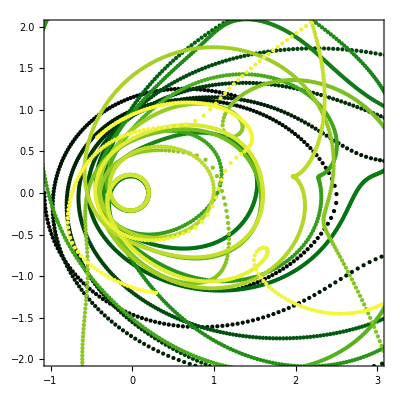

```mathematica
colfunc=ColorData["AvocadoColors"]; aa = 0;bb = 1600;
pts1=Table[{colfunc[(n-aa)/bb],Point[{Re[#],Im[#]}]}&/@zeros2[100, .5 + n*.02I],{n,aa,aa+bb}];
Graphics[pts1,Frame->True,PlotRange->{{-2+1,2+1},{-2,2}}]
```

```mathematica
ss[n_, s_] := Sum[ 2^(x(1-s))/x,{x,1,Log[2,n]}]
```

```mathematica
f[s_] := Sum[ k^-s, {k,1,5}]-1
```

```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FI[n]=FactorInteger[n];FI[1]:={}
Dz1[n_, z_, s_] := Dz1[n,z,s]=Sum[FullSimplify[ j^-s  dz[j,z]],{j,1,n}]
zerosd[n_,s_]:=List@@NRoots[Dz1[n,z,s]==0,z][[All,2]]
zerosdr[n_,s_]:=List@@Roots[Dz1[n,z,s]==0,z][[All,2]]
DxDAlt[n_,z_,x_,s_]:=Sum[(-1)^j bin[z,j] x^(j(1-s)) Dz1[n/x^j,z,s],{j,0,Log[x,n]}]
zerose[n_,s_]:=List@@NRoots[DxDAlt[n,z,2,s]==0,z][[All,2]]
zeroser[n_,s_]:=List@@Roots[DxDAlt[n,z,2,s]==0,z][[All,2]]
```

```mathematica
1-1/zerosd[30000,N[ZetaZero[1]]]
```

{1.01019+0.0246656 ⅈ,1.00576+0.0310077 ⅈ,1.01835+0.0754149 ⅈ,1.03902+0.144207 ⅈ,1.05578+0.294042 ⅈ,1.01884-0.257244 ⅈ,1.08487+0.684835 ⅈ,1.00305-0.133428 ⅈ,1.03747-0.606286 ⅈ,0.137877-2.31485 ⅈ,-0.421362+2.69743 ⅈ,0.994531-0.0594043 ⅈ,0.999821+0.00312797 ⅈ,0.992283-0.0168883 ⅈ}

```mathematica
1-1/zeros2[30000,N[ZetaZero[1]]]
```

{1.16051+0.0818891 ⅈ,-0.918653-3.93515 ⅈ,-0.00395532-0.00199566 ⅈ,0.46003-0.0130028 ⅈ,0.901701-0.18711 ⅈ,0.816009+0.220098 ⅈ,0.672987+0.104833 ⅈ,0.693862-0.0998235 ⅈ,0.980764+0.0388616 ⅈ,0.909317-0.0123339 ⅈ,0.934593-0.0120227 ⅈ,0.989332+0.0156057 ⅈ,0.982859-0.00641856 ⅈ,0.99883-0.00343033 ⅈ}

```mathematica
Dz1[10000,1,0]
```

10000

```mathematica
colfunc=ColorData["AvocadoColors"]; aa = 0;bb = 16;
pts1=Table[Point[{Re[#],Im[#]}]&/@zeros2[100, .5 + n*.02I],{n,aa,aa+bb}];
```

{{Point[{-1.07553,0}],Point[{1.30206,-1.15423}],Point[{1.30206,1.15423}],Point[{3.57559,0}],Point[{10.0652,-5.05697}],Point[{10.0652,5.05697}]},{Point[{-1.0748,-0.0456319}],Point[{1.2554,1.16747}],Point[{1.34863,-1.14}],Point[{3.57503,0.0136508}],Point[{10.0488,5.04717}],Point[{10.0817,-5.0668}]},{Point[{-1.07261,-0.0912289}],Point[{1.20867,1.17972}],Point[{1.39507,-1.12475}],Point[{3.57337,0.0272438}],Point[{10.0323,5.03739}],Point[{10.0982,-5.07665}]},{Point[{-1.06895,-0.136756}],Point[{1.1619,1.19099}],Point[{1.44135,-1.10846}],Point[{3.57059,0.0407208}],Point[{10.0158,5.02763}],Point[{10.1147,-5.08653}]},{Point[{-1.06384,-0.182179}],Point[{1.11513,1.20131}],Point[{1.48745,-1.09112}],Point[{3.5667,0.0540229}],Point[{9.99935,5.0179}],Point[{10.1312,-5.09643}]},{Point[{-1.05727,-0.227461}],Point[{1.06838,1.21067}],Point[{1.53334,-1.0727}],Point[{3.56169,0.0670898}],Point[{9.98289,5.0082}],Point[{10.1477,-5.10636}]},{Point[{-1.04925,-0.27257}],Point[{1.02168,1.21908}],Point[{1.57899,-1.05317}],Point[{3.55557,0.0798597}],Point[{9.96644,4.99852}],Point[{10.1642,-5.11631}]},{Point[{-1.03977,-0.31747}],Point[{0.97506,1.22654}],Point[{1.62439,-1.0325}],Point[{3.54832,0.0922685}],Point[{9.95,4.98886}],Point[{10.1807,-5.1263}]},{Point[{-1.02886,-0.362126}],Point[{0.928552,1.23306}],Point[{1.66952,-1.01066}],Point[{3.53994,0.104249}],Point[{9.93358,4.97922}],Point[{10.1972,-5.13631}]},{Point[{-1.01651,-0.406504}],Point[{0.882182,1.23865}],Point[{1.71435,-0.987593}],Point[{3.53043,0.115732}],Point[{9.91716,4.9696}],Point[{10.2137,-5.14634}]},{Point[{-1.00272,-0.45057}],Point[{0.835974,1.24329}],Point[{1.75887,-0.963267}],Point[{3.51977,0.126641}],Point[{9.90076,4.96001}],Point[{10.2302,-5.15641}]},{Point[{-0.987511,-0.494289}],Point[{0.789956,1.24701}],Point[{1.80307,-0.937627}],Point[{3.50795,0.136896}],Point[{9.88437,4.95045}],Point[{10.2467,-5.1665}]},{Point[{-0.970885,-0.537627}],Point[{0.74415,1.24978}],Point[{1.84695,-0.910616}],Point[{3.49497,0.14641}],Point[{9.86799,4.9409}],Point[{10.2632,-5.17662}]},{Point[{-0.952851,-0.580551}],Point[{0.698581,1.25163}],Point[{1.8905,-0.882165}],Point[{3.48081,0.155088}],Point[{9.85162,4.93138}],Point[{10.2796,-5.18676}]},{Point[{-0.93342,-0.623028}],Point[{0.65327,1.25254}],Point[{1.93372,-0.852198}],Point[{3.46545,0.162822}],Point[{9.83528,4.92188}],Point[{10.2961,-5.19694}]},{Point[{-0.9126,-0.665022}],Point[{0.60824,1.25252}],Point[{1.97661,-0.820624}],Point[{3.44886,0.169494}],Point[{9.81895,4.9124}],Point[{10.3126,-5.20714}]},{Point[{-0.890404,-0.706502}],Point[{0.563512,1.25157}],Point[{2.0192,-0.787333}],Point[{3.43103,0.174966}],Point[{9.80263,4.90295}],Point[{10.3291,-5.21738}]}}

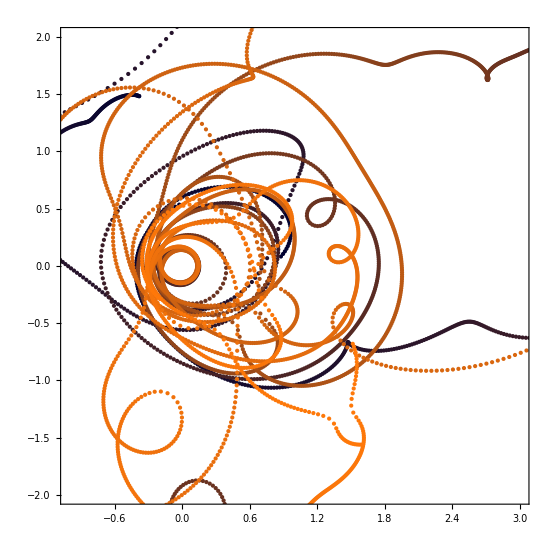

```mathematica
colfunc=ColorData["AlpineColors"]; aa = 0;bb = 1600;
pts1=Table[{colfunc[(n-aa)/bb],Point[{Re[#],Im[#]}]}&/@zeros2[100, -.1+n*.02I+N[ZetaZero[12]]],{n,aa,aa+bb}];
Graphics[pts1,Frame->True,PlotRange->{{-2+1,2+1},{-2,2}}]
```

```mathematica
colfunc=ColorData["AlpineColors"]; aa = 0;bb = 1600;
pts1=Table[{colfunc[(n-aa)/bb],Point[{Re[#],Im[#]}]}&/@zeros2[1000, -.1+n*.02I+N[ZetaZero[12]]],{n,aa,aa+bb}];
Graphics[pts1,Frame->True,PlotRange->{{-2+1,2+1},{-2,2}}]
```

$Aborted

$Aborted[]